```mathematica
g2[r_,β_,α_]:=(((1-r^β)/β)^α-1)/α
```

```mathematica
cK={{-21.589968,-62.8742},{0.000796839,1.3060},{-21.259381,-85.4861},{0.000558969,-8.3589}}
β={-10.058835,-9.1435}
α={-0.34055399,-0.3900}
```

{{-21.59,-62.8742},{0.000796839,1.306},{-21.2594,-85.4861},{0.000558969,-8.3589}}

{-10.0588,-9.1435}

{-0.340554,-0.39}

"{", 

  RowBox[{

   RowBox[{"-", "3.9824`"}], ",", 

   RowBox[{"-", "3.9824`"}]}], "}"}]], "Output",

 CellChangeTimes->{{3.8535901286783786`*^9, 3.853590148058016*^9}, 

   3.8535976056644187`*^9, 3.85377221318692*^9, 3.853843489743413*^9, 

   3.853844485452462*^9, 3.8538449585151978`*^9, 3.8538449995224147`*^9, 

   3.8538451340163345`*^9},

 CellLabel->

  "Out[134]=",ExpressionUUID->"60396f71-6095-4643-9387-c5297df9603b"],



Cell[BoxData[

 RowBox[{"{", 

  RowBox[{

RowBox[{"-", "0.3123`"}], ",", 

   RowBox[{"-", "0.3883`"}]}], "}"}]], "Output",

 CellChangeTimes->{{3.8535901286783786`*^9, 3.853590148058016*^9}, 

   3.8535976056644187`*^9, 3.85377221318692*^9, 3.853843489743413*^9, 

   3.853844485452462*^9, 3.8538449585151978`*^9, 3.8538449995224147`*^9, 

   3.853845134019337*^9},

 CellLabel->

  "Out[135]=",ExpressionUUID->"b20468c9-ca6f-4e98-9025-5208d5c90342"]

}, Open  ]],



Cell[CellGroupData[{



Cell[BoxData[

 RowBox[{

```mathematica
fK[t_,T_]={cK[[1,1]]+cK[[2,1]]((Log[t]-cK[[3,1]])/((1/T)-cK[[4,1]])),
cK[[1,2]]+cK[[2,2]]((Log[t]-cK[[3,2]])/(Log[(1/T)]-cK[[4,2]]))}
```

{-21.59+(0.000796839 (21.2594+Log[t]))/(-0.000558969+1/T),-62.8742+(1.306 (85.4861+Log[t]))/(8.3589+Log[1/T])}

```mathematica
Ketlnt[t_,T_]=Table[Solve[fK[t,T][[i]]==g2[r,β[[i]],α[[i]]],Log[t]][[1,1,2]],{i,1,2,1}]-Log[3600]
```

{1254.96 (21.59-2.93639 (-1.+2.19493/((-1.+1/r^10.0588)^0.340554))-0.0169403/(-0.000558969+1/T)) (-0.000558969+1/T)-Log[3600],-Log[3600]+0.765697 (8.3589+Log[1/T]) (62.8742-2.5641 (-1.+2.37047/((-1.+1/r^9.1435)^0.39))-111.645/(8.3589+Log[1/T]))}

```mathematica
Kettblr=Table[Table[Ketlnt[t,T][[i]],{r,{0.55,0.93}}],{i,1,2,1}]
KetpseudoFA=Simplify[Table[Kettblr[[1,i]],{i,1,2,1}]]/. 1/T->10^-3 T;
KetpseudoFCA=Simplify[Table[Kettblr[[2,i]],{i,1,2,1}]]/. 1/T->10^-3 T;
```

{{1254.96 (23.6942-0.0169403/(-0.000558969+1/T)) (-0.000558969+1/T)-Log[3600],1254.96 (18.238-0.0169403/(-0.000558969+1/T)) (-0.000558969+1/T)-Log[3600]},{-Log[3600]+0.765697 (8.3589+Log[1/T]) (64.7161-111.645/(8.3589+Log[1/T])),-Log[3600]+0.765697 (8.3589+Log[1/T]) (59.216-111.645/(8.3589+Log[1/T]))}}

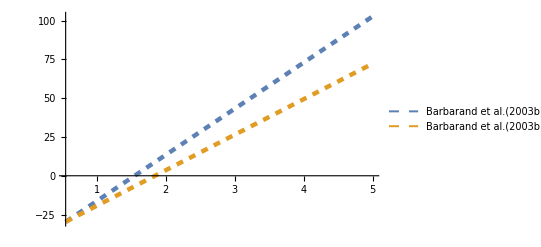
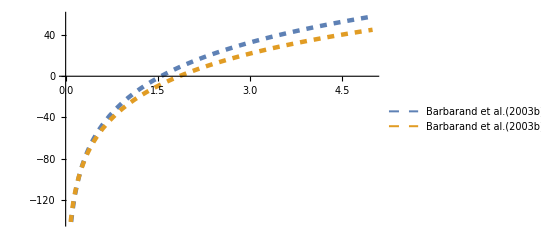

```mathematica
pltPseudoArrheniusKet={Plot[KetpseudoFA,{T,0.55,5},PlotStyle->{{Dashed,Thickness[0.0080]}},LabelStyle->Directive[FontSize->18],PlotLegends->Placed[{"Barbarand et al.(2003b)","Barbarand et al.(2003b)"},{0.6,0.2}]],Plot[KetpseudoFCA,{T,0.,5},PlotStyle->{{Dashed,Thickness[0.0080]}},LabelStyle->Directive[FontSize->18],PlotLegends->Placed[{"Barbarand et al.(2003b)","Barbarand et al.(2003b)"},{0.6,0.2}]]}
```